# Feasible Sets

Unconstrained optimization
	min f(x) 
is easier than equality constrained optimization
	min_(g_e(x)=OverVector[0]) f(x)
is easier than inequality constrained optimization
	min_(g_i(x)≥OverVector[0]) f(x)
is easier than the general constrained optimization
	min_(g_e(x)=OverVector[0]
g_i(x)≥OverVector[0]) f(x)
In the above, the scalar cost function 
	f:ℝ^n→ℝ
will be smooth as will the vector constraint functions
	g_e:ℝ^n→ℝ^m_e and g_i:ℝ^n→ℝ^m_i 
The numbers m_e and m_i are how many equality and inequality constraints there are.  More than n equality constraints does not make sense.  Any number of inequality constraints makes sense!

The set of points satisfying the constraints
	g_e(x)=OverVector[0]
g_i(x)≥OverVector[0]
is called the feasible set. The first task of any constrained optimization algorithm is to find an element of the feasible set!

## Plotting Low-Dimensional Feasible Sets

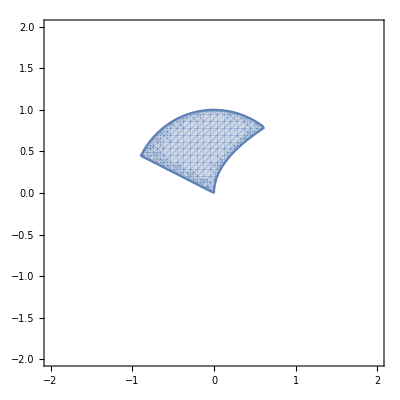

```mathematica
gi[{x1_,x2_}]:=And[1-(x1^2+x2^2)>0,x1+2 x2>0,x2^2-x1>0]
RegionPlot[gi[{x1,x2}],{x1,-2,2},{x2,-2,2},PlotPoints->50]
```

```mathematica
gi[{x1_,x2_,x3_}]:=And[1-(x1^2+x2^2)>0,x1+2 x2^2-x3>0,1-x3-x1>0,x3^3+x2+1>0]
RegionPlot3D[gi[{x1,x2,x3}],{x1,-2,2},{x2,-2,2},{x3,-2,2},PlotPoints->10^2]
```

-Graphics3D-

## Cusps and Corners

Hopefully it is clear that the feasible set can have corners and pointy bits! Hopefully it is clear that the feasible region could be unbounded! Corners will not be a problem.  Cusps will be assumed away!

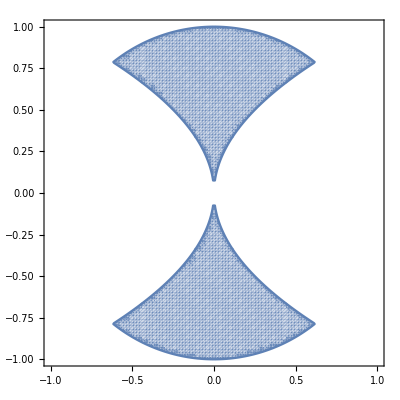

```mathematica
gi[{x1_,x2_}]:=And[1-(x1^2+x2^2)≥0,x2^2-x1≥0,x2^2+x1≥0]
RegionPlot[gi[{x1,x2}],{x1,-1,1},{x2,-1,1},PlotPoints->10^2]
```

## Higher Dimensions

In higher dimensions there is no way to plot the feasible region.  In general, there is no practical way to work out what the feasible region looks like.